ⅇ^(InverseErf[t]^2)

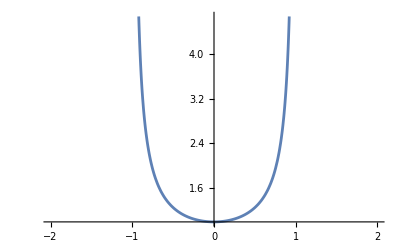

```mathematica
y[t_]=Exp[InverseErf[t]^2]
Show[Plot[y[t],{t,-2,2}]]
```

```mathematica
(*Define the convolution over the valid domain*)
y[t_]:=Exp[InverseErf[t]^2] UnitStep[1-t] UnitStep[t+1]
conv[x_]:=Convolve[y[t],y[t],t,x]
convSimplified=FullSimplify[conv[x],Assumptions->Element[x,Reals]]
```

Piecewise[{{Convolve[ⅇ^(InverseErf[t]^2),ⅇ^(InverseErf[t]^2),t,x], -1≤t≤1}, {0, True}}]

```mathematica
Plot[conv[x],{x,-2,2},PlotRange->All,PlotLabel->"Self-Convolution using Convolve[]",AxesLabel->{"x","y*y(x)"}]
```

-Graphics-

```mathematica
Plot[yCon,{tau,-2,2}]
```